## Tents, Humps, and Wiggles

Split an interval 0≤x≤L up with m equally spaced internal points
	x_i=i h
where h=L/(m+1) and build a variety of piecewise polynomial nodal functions.

### Tents

Piecewise linear functions are represented by tent functions.

One way to think abut computing the formula is by matching the 4 coefficients in a piecewise linear function
	L(x)=Piecewise[{{-h<x<0, a0+a1 x}, {0<x<h, b0+b1 x}}]
and match the conditions L continuous at -h, h, and 0 and L[0]=1.  These 4 conditions in the four unknowns completely determine the Tent function. Should I do a reference element and scale and shift?

```mathematica
{a0+a1 x, b0 + b1 x}/.Solve[{a0==1,b0==1,a0 - a1 h ==0, b0+b1 h ==0  }]
```

{{1+x/h,1-x/h}}

```mathematica
Lin[x_]:= Piecewise[{
{1+x,-1<x<0},
{1-x,0<x<1}
},0]
dLin[x_]:= Piecewise[{
{1,-1<x<0},
{-1,0<x<1}
},0]
(*Tent[i_,h_][x_]:= Piecewise[{
{1.0 +(x- i h)/h,(i-1)h<x<i h},
{1.0-(x-i h)/h,i h<x<(i+1)h}
},0]*)
Tent[i_,h_][x_]:=Lin[(x-i h)/h]
dTent[i_,h_][x_]:=1/h dLin[(x-i h)/h]
{L,m}={π,5}; h=L/(m+1.0);
f[x_]:=Sin[x]
us=Table[ f[i h],{i,1,m}]; u[x_]=Sum[us⟦i⟧Tent[i,h][x],{i,1,m}];
TabView[{
"Tents"->Plot[{Tent[1,h][x],Tent[2,h][x]},{x,0,L},
PlotRange->All],
"Interpolation"->Plot[{f[x],u[x]},{x,0,L}]}]
```

12

### Humps and Wiggles

One way to think abut computing the formula is by again matching coefficients in a piecewise polynomial function to satisfy
	P is continuous at -h, h, and 0.
	P' is continuous at -h, h, and 0
and some values P(0) and P'(0) for matching the 8 coefficients in a piecewise cubicic function
	P(x)=Piecewise[{{-h<x<0, a0+a1 x+a2 x^2+a3 x^3}, {0<x<h, b0+b1 x+ b2 x^2+b3 x^3}}]
and match the conditions P and P' continuous at -h, h, and 0 and P[0]=1.   I can scale and shift to build these functions out of the ones defined by h=1.

```mathematica
Clear[a0,a1,a2,a3,b0,b1,b2,b3]
Qa[x_]:=a0+a1 x + a2 x^2+a3 x^3; Qb[x_]:=b0+b1 x + b2 x^2+b3 x^3
Eqv={
Qa[0]==Qb[0]==1,
Qa'[0]==Qb'[0]==0,
Qa[-1]==0, Qa'[-1]==0,
Qb[1]==0, Qb'[1]==0}
{Qa[x],Qb[x]}/.Solve[Eqv,{a0,a1,a2,a3,b0,b1,b2,b3}];
Eqs={
Qa[0]==Qb[0]==0,
Qa'[0]==Qb'[0]==1,
Qa[-1]==0, Qa'[-1]==0,
Qb[1]==0, Qb'[1]==0};
{Qa[x],Qb[x]}/.Solve[Eqs,{a0,a1,a2,a3,b0,b1,b2,b3}]
```

{a0==b0==1,a1==b1==0,a0-a1+a2-a3==0,a1-2 a2+3 a3==0,b0+b1+b2+b3==0,b1+2 b2+3 b3==0}

{{x+2 x^2+x^3,x-2 x^2+x^3}}

```mathematica
CubeV[x_]:= Piecewise[{
{1-3 x^2-2 x^3, -1<x≤0},
{1-3 x^2+2 x^3, 0<x<1}
},0]
CubeS[x_]:= Piecewise[{
{x+2 x^2+x^3, -1<x≤0},
{x-2 x^2+x^3, 0<x<1}
},0]
dCubeV[x_]:= Piecewise[{
{6x-6 x^2, -1<x≤0},
{6x+6 x^2, 0<x<1}
},0]
dCubeS[x_]:= Piecewise[{
{1+4x+3 x^2, -1<x≤0},
{1-4x+3 x^2, 0<x<1}
},0]
ddCubeV[x_]:= Piecewise[{
{6-12x, -1<x≤0},
{6+12x, 0<x<1}
},0]
ddCubeS[x_]:= Piecewise[{
{4+6x, -1<x≤0},
{-4+6x, 0<x<1}
},0]
TabView[{
"f"->Plot[{CubeV[x],CubeS[x],Lin[x]},{x,-1,1},PlotRange->All],
"f'"->Plot[{dCubeV[x],dCubeS[x],dLin[x]},{x,-1,1},PlotRange->All],
"f''"->Plot[{ddCubeV[x],ddCubeS[x]},{x,-1,1},PlotRange->All]
}]
```

123

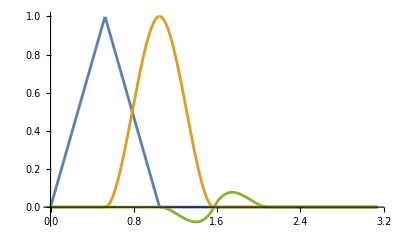

```mathematica
Tent[i_,h_][x_]:= Lin[x/h-i]
Hump[i_,h_][x_]:=CubeV[x/h-i]
Wiggle[i_,h_][x_]:=h CubeS[x/h-i]

{L,m}={π,5}; h=L/(m+1.0);
Plot[ {Tent[1,h][x],Hump[2,h][x],Wiggle[3,h][x]},{x,0,L},PlotRange->All]
```

## Guitar Strings

### FD Dirichlet-Dirichlet

The weak form for -k u''=f is 
	k∫_0^L u' v'=∫_0^L f v.  
The weak form for ρ u_tt=-k u_xx is  
	∫_0^L ρ u_tt v=k∫_0^L v_x u_x.
with the shape functions {Tent[i,h][x]}_(i=1)^n the stiffness matrix is defined by
	A_ij=∫_0^L v_x u_x dx
where u=Tent[i,h][x] and v=Tent[j,h][x] .  The matrix is clearly symmetric. The first derivatives are piecewise constant
	Tent[i_,h_][x_]:= Lin[x/h-i]
	The non-zero constant sections overlap iff i=j or i=j±1

```mathematica
dTent[i_,h_][x_]:= 1/h dLin[x/h-i]
```

```mathematica
1.0 (m+1)/L
Tent[1,h]'[x]
```

1.90986

Piecewise[{{0, x<0}, {1.90986, 0<x<26714619/51021164}, {-1.90986, 26714619/51021164<x<26714619/25510582}, {0, x>26714619/25510582}, {Indeterminate, True}}]

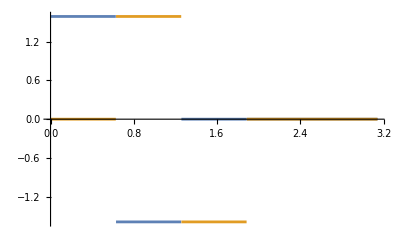

```mathematica
Plot[{Tent[1,h]'[x],Tent[2,h]'[x]},{x,0,L}]
```

```mathematica
Clear[m]
m=4;
h=L/(m+1);
Integrate[Tent[i,h]'[x]*Tent[j,h][x],{x,0,L}]
```

$Aborted

#### Second order FD.

```mathematica
n=48;h=π/(n+1); 
A=1.0/h^2 SparseArray[{Band[{1,1}]->2,Band[{1,2}]->-1, Band[{2,1}]->-1},{n,n}];
λs=Reverse[Eigenvalues[A,-20]];
ListLogLogPlot[{λs, Table[i^2,{i,20}]},Joined->{False,True},
PlotLabel->λs⟦1;;5⟧]
```

#### 4th order FD.

```mathematica
Clear[f,x,dx]
ResourceFunction["FiniteDifferenceStencil"][f''[x],{f[x-2dx],f[x-dx],f[x],f[x+dx],f[x+2dx]},f,x]
n=48;h=π/(n+1); 
A=1.0/h^2 SparseArray[{
Band[{1,1}]->5/2,
Band[{1,2}]->-4/3, Band[{2,1}]->-4/3,
 Band[{1,3}]->1/12,Band[{3,1}]->1/12},{n,n}];
λs=Reverse[Eigenvalues[A,-20]];
ListLogLogPlot[{λs, Table[i^2,{i,20}]},Joined->{False,True},
PlotLabel->λs⟦1;;5⟧]
```

#### 6th order FD.

```mathematica
Clear[f,x,dx]
ResourceFunction["FiniteDifferenceStencil"][f''[x],{f[x-3dx],,f[x-2dx],f[x-dx],f[x],f[x+dx],f[x+2dx],f[x+3dx]},
f,x]
n=48;h=π/(n+1); 
A=1.0/h^2 SparseArray[{
Band[{1,1}]->49/18,
Band[{1,2}]->-3/2, Band[{2,1}]->-3/2,
 Band[{1,3}]->3/20,Band[{3,1}]->3/20,
 Band[{1,4}]->-1/90,Band[{4,1}]->-1/90
},{n,n}];
λs=Reverse[Eigenvalues[A,-20]];
ListLogLogPlot[{λs, Table[i^2,{i,20}]},Joined->{False,True},
PlotLabel->λs⟦1;;5⟧]
```

### FE Dirichlet-Dirichlet

The weak form is ∫_0^π u'(x)v'(x)dx

#### Fourier Basis

The Fourier basis sin(i x) satisfies D-D boundary conditions and gives a diagonal stiffness matrix.

```mathematica
n=6;
ϕ[i_][x_]:=√(2/π)Sin[i x]
Plot[{ϕ[1][x],ϕ[2][x],ϕ[3][x],ϕ[4][x]},{x,0, π}]
A=Table[ Integrate[ϕ[i]'[x]ϕ[j]'[x],{x,0, π}],
{i,n},{j,n}]
```

It is hard to compute the zero entries numerically.

```mathematica
n=6
AbsoluteTiming[
Quiet[
A=Table[ NIntegrate[ϕ[i]'[x]ϕ[j]'[x],{x,0, π}],
{i,n},{j,n}]
];
]
Eigenvalues[A]
```

#### Tent Basis

The Tent basis gives a tridiagonal stiffness matrix. The tents at the interior modes satisfy D-D conditions. It is a bit crazy to do the integration.  The superposition of these tent function linearly interpolates the weights at the nodes.

```mathematica
n=6;
ϕ[i_,n_][x_]:=Piecewise[{
{1+n(x/π-i/n),(i-1)/n<x/π< i/n },
{1-n(x/π-i/n), i/n<x/π< (i+1)/n }
},0]
Plot[{ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

The integrands for the stiffness functions are piecewise constant! Integrate and NIntegrate work fine.

```mathematica
n=12;
AbsoluteTiming[
A=Table[ NIntegrate[ϕ[i,n]'[x]ϕ[j,n]'[x],{x,0, π}],
{i,n},{j,n}];
]
MatrixPlot[A]
Eigenvalues[1.0*A]
```

#### Polynomial Basis: Mark 1

The polynomial basis 
	x (x/π-i/n)(x-π)
that got dreamed up should not work. They are all combinations of x,x^2,and x^3.

```mathematica
ϕ[i_,n_][x_]:=x(x-(i π)/n)(x-π)
n=5;
Plot[{ϕ[0,n][x],ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

The integrands for the stiffness functions are polynomials! Integrate works fine for small systems but will get slow for big systems. NIntegrate complains about some zero entries and will get slow for large systems.

```mathematica
n=12;
A=1.0*Table[ Integrate[ϕ[i,n]'[x]ϕ[j,n]'[x],{x,0, π}],
{i,0,n},{j,0,n}];
Eigenvalues[A]
```

#### Polynomial Basis: Mark 2

The polynomial basis 
	x (π_(j=1)^(n-1)(x/π-j/(n+1)))/(x/π-i/(n+1))(x-π)=
that got dreamed up should work. They are LI.

```mathematica
ϕ[i_,n_][x_]:=x Product[(x/π-j/(n+1)),{j,1,i-1}]Product[(x/π-j/(n+1)),{j,i+1,n}](x-π)
n=5;
Plot[{ϕ[0,n][x],ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

Thing is we might as well use the easier basis 
	x*x^i*(x-π)
for i=0,1,2,3,n-1.  The funny normalization makes ∫ϕ^2=1

```mathematica
Clear[i,n,x]
ϕ[i_][x_]:=√((30+47 i+24 i^2+4 i^3)/π^(5+2 i))x*x^i*(x-π)
Plot[{ϕ[0][x],ϕ[1][x],ϕ[2][x],ϕ[3][x],ϕ[4][x],ϕ[5][x]},{x, 0 ,π},PlotRange->All]
```

```mathematica
n=12;
A=1.0*Table[ Integrate[ϕ[i]'[x]ϕ[j]'[x],{x,0, π}],
{i,0,n},{j,0,n}];
Eigenvalues[A]
```

## Beam Strings

#### Fourier Bi-Bi Basis

```mathematica
ϕ[i_][x_]:=√(60/π^5)x Sin[i x](x-π)
Clear[i,j]
Integrate[ ϕ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
Integrate[ ϕ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
FullSimplify[Integrate[ ϕ[i][x]ϕ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
```

```mathematica
Plot[ Evaluate[Table[ϕ[i][x],{i,1, 7}]],{x,0,π},
PlotLegends->Automatic]
```

#### Fourier SS-SS Basis

```mathematica
ϕ[i_][x_]:=√(60/π^5)x Sin[i x](x-π)
ψ[i_][x_]:=√(60/π^5)x Cos[i x](x-π)
Clear[i,j]
FullSimplify[Integrate[ ϕ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
Integrate[ ϕ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
FullSimplify[Integrate[ ϕ[i][x]ϕ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ψ[i]''[x]ψ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
Integrate[ ψ[i]''[x]ψ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
FullSimplify[Integrate[ ψ[i][x]ψ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
```

```mathematica
FullSimplify[Integrate[ ψ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ψ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)} ]
```

```mathematica
n=3 10^3;
A=RandomReal[{-1,1},{n,n}];
AbsoluteTiming[λ=Eigenvalues[A];]
```

```mathematica
Plot[ Evaluate[Table[ϕ[i][x],{i,1, 7}]],{x,0,π},
PlotLegends->Automatic]
Plot[ Evaluate[Table[ψ[i][x],{i,0, 7}]],{x,0,π},
PlotLegends->Range[0,7]]
```

#### Fourier Bi-Bi Kalimba Basis

Think about this!

```mathematica
ϕ[i_][x_]:=x Sin[i x](x-a)(x-π)
Clear[i,j]
FullSimplify[Integrate[ ϕ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ϕ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ϕ[i][x]ϕ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
```

```mathematica
a=1.2;
Plot[ Evaluate[Table[ϕ[i][x],{i,1, 7}]],{x,0,π},
PlotLegends->Automatic]
```

#### Beam “Tent” aka piecewise “humps and wiggles” Basis

Explain why?

```mathematica
Clear[p1,p2]
p1[h_][x_]=x^2(a0 + a1 x)(x-2h)^2
p2[h_][x_]=x^2(b0 + b1 x)(x-2h)^2
Simplify[{p1[h][h]==1, p1[h]'[h]==0}]
Simplify[{p2[h][h]==0, p2[h]'[h]==1}]
```

So a1 = 0 and a0=1/h^4.
So b1 = 1/h^4 and b0=-1/h^3

```mathematica
p1[h_][x_]=Simplify[x^2(1/h^4 + 0 x)(x-2h)^2]
p2[h_][x_]=Simplify[x^2(-1/h^3+1/h^4 x)(x-2h)^2]
Plot[{p1[1][x],p2[1][x]},{x,0, 2}]
```

Could put more Degrees of Freedom (DOF) inside each interval using polynomials or sines.  More DOF would mean we could have bigger intervals that would mean more possible whammy bar movement.

```mathematica
(* Hump functions *)
(* NOTE: I ended up paramatarizing both sets of functions a lot more than you did just to make the process a little more clear to me - let me know if you'd like me to clean them up a bit more! *)
```

```mathematica
n=5;
L = Pi;
h = L/(n+1);
ϕ[i_,n_][x_]:=Piecewise[{
{(x-(i-1)*L/(n+1))^2((x-(i-1)*L/(n+1))-2h)^2/h^4,(i-1)h<x< (i+1)*h }
},0]
Plot[{ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

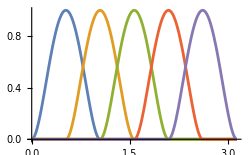
```mathematica
-Graphics-

(* Wiggle functions *)
ϕ[i_,n_][x_]:=Piecewise[{
{(x-(i-1)*L/(n+1))^2((x-(i-1)*L/(n+1))-2h)^2(-1/h^3+(x-(i-1)*L/(n+1))/h^4),(i-1)h<x< (i+1)*h }
},0]
Plot[{ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

Building Block matrices.

```mathematica
A11= RandomReal[{0,1},{3,4}];
A12= RandomReal[{-1,0},{3,6}];
A13= RandomReal[{2,6},{3,7}];
A21= RandomReal[{-1,1},{4,4}];
A22= RandomReal[{-1,1},{4,6}];
A= ArrayFlatten[ {
{A11, A12, A13},
{A21, A22, 0}
}];
MatrixPlot[A]
```

The integrands for the stiffness functions are ! Integrate and NIntegrate work fine.

```mathematica
n=12;
AbsoluteTiming[
A=Table[ NIntegrate[ϕ[i,n]'[x]ϕ[j,n]'[x],{x,0, π}],
{i,n},{j,n}];
]
MatrixPlot[A]
Eigenvalues[1.0*A]
```

## Possibilities

Possibilities

1) Explainer for Guitar Strings
Target Audience ODE Class Lin Alg background

2) Explainer for BI-BI Beam
Target Audience ODE Class Lin Alg background

3) Kalimba
Target Audience ODE Class Lin Alg background

4) Tuning shaped beams  “Marimba”
Target Audience ODE Class Lin Alg background

Questions:
Physics equations explained or not. 
Data?
Guitar FE and/or FD?
BI-BI beam FE and/or FD?
Kalimba and Marimba FE?

Audio output?
Animation output?
Delivery mechanism? 

∂_xx (a(x) ∂_xx u) =  ±  b(x) u_tt
u_xxxx=± u_tt

weak or variational form or virtual displacement 

∫∂_xx (a(x) ∂_xx u) v(x) dx  =  ±  ∫ b(x) v(x) u_tt dx
∫a(x) ∂_xx u v_xx(x) dx  + Boundary Terms =  ±  ∫ b(x) v(x) u_tt dx

∫ u_xx v_xx dx= κ∫v u_tt dx

```mathematica
{a1,a2,a3,a4,a5}={1.1,-2.1,0.3,0.4,0.4}
u[x_,t_]:= a1 Cos[ 1000 t] Sin[1 x]+ a2 Cos[ 2000 t] Sin[2 x]+ a3 Cos[ 3000 t] Sin[3 x]+ a4 Cos[ 4000 t] Sin[4 x]+ a5 Cos[12000 t] Sin[12 x]
Plot[u[x,0],{x,0, π}];
Manipulate[ Plot[u[x,t],{x,0, π},PlotRange->{-4,4}],{t,0, 12/1000,0.1/1000}]
Play[u[π/2,t],{t,0, 3}]
Play[u[1.0,t],{t,0, 3}]
```